## 1. 问卷数据导入与品质分析

### 1.1. 问卷Excel导入为Mathematica的嵌套List函数式

```mathematica
ansRaw=Import[NotebookDirectory[]<>"285334255_00001-00078.xlsx","XLSX"]//First;
```

```mathematica
ansRaw//Dimensions
```

{79,105}

Excel每列字段名称提取

```mathematica
ansFields=ansRaw[[1,All]];
MapIndexed[{#2[[1]],#1}&,ansFields]//Grid[#,Alignment->Left]&//Pane[#,{800,300},Scrollbars->{False,True}]&//CreateDialog;
```

### 1.2. 答题时长分析

```mathematica
ansDuration=StringReplace[#,"秒"->""]&/@ansRaw[[2;;,3]];
ansDuration=ToExpression/@ansDuration;
```

### 1.2.1. 基本统计量

```mathematica
Table[stat[ansDuration],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{422.808,962.359,8.33195,72.2406}

结果严重正偏, √M_2, M_3, M_4统计结果受极端值影响严重.

需要检测答题时长的离群值, 在将其移除后重新进行统计.

#### 1.2.2. 异常值检测与移除

依据: Med ± 1.5·QI范围外的值为异常值, Med ± 3·QI范围外的值为严重异常值, 其中QI=Q_3-Q_1

```mathematica
ansDuraMed=ansDuration//Median
```

579/2

```mathematica
ansDuraQI=ansDuration//Quantile[#,{1/4,3/4}]&//Differences//First
```

197

```mathematica
ansDuraOU=Select[ansDuration,#≥ansDuraMed+1.5ansDuraQI&]
```

{8707,759,762,752,634}

```mathematica
ansDuraFOU=Select[ansDuration,#≥ansDuraMed+3ansDuraQI&]
```

{8707}

```mathematica
ansDuraOL=Select[ansDuration,#≤ansDuraMed-1.5ansDuraQI&]
```

{}

异常高值5个, 均大于600s(10 min), 其中最大值为8707s(折合约2 hr 25 min), 超出Med±3·QI范围; 其余异常值均介于600s(10 min)至900s(15 min)之间, 在Med±3·QI范围以内. 
可能原因推测: 受访者在网络答题过程中因为工作事务中断答题, 下工后提交问卷. 
异常低值0个. 
据此, 无法通过单纯分析异常低值(答题速度异常偏快)判定答卷作答是否出现胡乱填写的情况, 需结合特定问题的答题特征判定.

移除异常值后重新统计

```mathematica
ansDurationRmOtl=Select[ansDuration,Abs[(#-ansDuraMed)/ansDuraQI]<1.5&];
```

```mathematica
Table[stat[ansDurationRmOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{292.671,121.749,0.45053,2.49457}

```mathematica
ansDurationRmFarOtl=Select[ansDuration,Abs[(#-ansDuraMed)/ansDuraQI]<3&];
```

```mathematica
Table[stat[ansDurationRmFarOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{315.221,153.61,1.01363,3.88611}

```mathematica
PairedHistogram[ansDurationRmOtl,ansDurationRmFarOtl,{0,900,30},AxesOrigin->{0,0},Ticks->{Range[0,10,5],Range[0,900,150]}]
```

-Graphics-

分别筛除Med±1.5·QI和Med±3·QI的结果, 分别显示作答时长分布呈正偏特征. 进一步分析: 部分受访者作答时长(介于600s至900s)可能非异常值. 
可能原因推测: 1. 问卷题目设置较多, 题目被排版至多个页面, 拖慢部分受访者答题进度. 
2. 问卷中排序题, 量表题比例较大, 由于问卷在线上填写, 大量受访者在答题后期出现疲劳, 加快答题速度.

### 1.3. 排序题质量检测方法

#### 1.3.1. 排序题排序指数

由于问卷题量和排序题比例较大, 受访者可能在尽快完成作答的动机下, 顺次点选排序题中的若干选项. 
问卷发布早期, 部分排序题未设置”选项乱序显示”功能, 前期接收的部分问卷, 对应排序题中的答案可能出现正序排列的现象. 
问卷发布后, 在2024-10-15 15:30(北京时间)许, 对14, 15题启用”选项乱序显示”, 其他排序题的选项显示模式未作变动, 启用前, 已收集31份答卷. 
据此: 可引入一种基于”排序不等式”的指数, 分析用户在排序题中的行为.

```mathematica
seqIndex//Clear;
seqIndex[seq_]:=Block[{nOptn,nOptnSel,seqAsc,seqRnd,seqDesc,phase,sumSortOrd,sumInvOrd,sumRndOrd,seqIdx},
	nOptn=Length[seq];
	seqRnd=Cases[seq,Except[""]];nOptnSel=Length[seqRnd];
	seqDesc=Sort[seqRnd,Greater];seqAsc=Reverse[seqDesc];
	phase=Range[nOptnSel];
	sumSortOrd=seqAsc.phase;sumInvOrd=seqDesc.phase;sumRndOrd=seqRnd.phase;
	If[sumSortOrd==sumInvOrd,Return[0];];
	seqIdx=(sumRndOrd-sumInvOrd)/(sumSortOrd-sumInvOrd);
	seqIdx=(2*seqIdx-1)*nOptnSel/nOptn;
	Return[seqIdx];
]
```

问卷的9, 10, 14, 15题均为排序题, 计算每位受访者在4道排序题的排序指数

```mathematica
ans09SeqIdx=seqIndex/@ansRaw[[2;;,45;;53]];
ans10SeqIdx=seqIndex/@ansRaw[[2;;,54;;59]];
ans14SeqIdx=seqIndex/@ansRaw[[2;;,72;;78]];
ans15SeqIdx=seqIndex/@ansRaw[[2;;,79;;85]];
```

```mathematica
ansSeqIdx={ans09SeqIdx,ans10SeqIdx,ans14SeqIdx,ans15SeqIdx}//Transpose;
```

#### 1.3.2. 排序题排序指数统计分析

对全体问卷, 计算不同排序题排序指数之间的相关系数.

```mathematica
ansSeqIdx//Correlation//MatrixForm
```

(1. | 0.0916738 | 0.195416 | 0.226391
0.0916738 | 1. | -0.169535 | 0.0910686
0.195416 | -0.169535 | 1. | 0.464177
0.226391 | 0.0910686 | 0.464177 | 1.)

对第1~31份问卷, 和第32~78份问卷的排序指数, 分别统计相关系数. 
依据: 前31份问卷的四道排序题均未启用”选项乱序显示”功能; 自第32份问卷起, 对第14, 15题启用”选项乱序显示”, 第9, 10题不启用.

```mathematica
ansSeqIdx[[;;31]]//Correlation//MatrixForm
```

(1. | 0.184699 | 0.384031 | 0.405116
0.184699 | 1. | -0.39325 | -0.0639138
0.384031 | -0.39325 | 1. | 0.54261
0.405116 | -0.0639138 | 0.54261 | 1.)

```mathematica
ansSeqIdx[[32;;]]//Correlation//MatrixForm
```

(1. | 0.00953888 | 0.0389687 | 0.0793816
0.00953888 | 1. | 0.0452229 | 0.251911
0.0389687 | 0.0452229 | 1. | 0.392341
0.0793816 | 0.251911 | 0.392341 | 1.)

第14, 15题间的排序指数相关关系较其他排序题间的关系更为显著, 且为正相关关系. 
可能原因推测: 两题均涉及游客对东湖绿道内导览设施的使用调查. 两道排序题连续出现; 调查内容相似, 但问题面向的情景不同; 选项种类和数量相同; 上述因素共同作用, 导致受访者答题时出现疲劳, 通过顺次选择选项的手段加快答题速度.

计算各排序题排序指数与作答时长的相关系数:

```mathematica
MapThread[Flatten[{##1}]&,{ansSeqIdx,ansDuration}]//Correlation//Last//Most//MatrixForm
```

(-0.305022
0.196317
-0.243674
-0.13301)

#### 1.3.3. 排序题异常结果提取

对所有问卷所有排序题的排序指数执行主成分正变换, 取第一主成分:

```mathematica
ansSeqIdxPC1=PrincipalComponents[ansSeqIdx][[All,1]];
```

筛除异常值

```mathematica
ansSeqIdxPC1Med=ansSeqIdxPC1//Median
```

0.0797231

```mathematica
ansSeqIdxPC1QI=ansSeqIdxPC1//Quantile[#,{1/4,3/4}]&//Differences//First
```

0.520372

```mathematica
ansSeqIdxPC1Outlier=Select[ansSeqIdxPC1,Abs[(#-ansSeqIdxPC1Med)/ansSeqIdxPC1QI]≥1.5&]
```

{-0.943832,0.870831,-0.949291,-0.913279,-0.989083,-0.767153,-0.701592}

共计7个异常值.

确认异常值所在的问卷编号

```mathematica
ansOutlierIdx=Position[ansSeqIdxPC1,_?(Abs[(#-ansSeqIdxPC1Med)/ansSeqIdxPC1QI]≥1.5&)]
```

{{2},{5},{15},{21},{69},{70},{75}}

#### 1.3.4. 排序题异常结果筛除比对

统计排序题

```mathematica
rankingMatrix//Clear;
rankingMatrix[ans_]:=Block[{nOptn,ord,matOrd},
	nOptn=ans[[1]]//Length;
	ord=ans//Transpose;
	matOrd=Table[Count[ord[[idxItem]],idxOrd//N],{idxItem,nOptn},{idxOrd,nOptn}];
	Return[matOrd];
];
```

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,45;;53]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{42 | 7 | 0 | 1 | 1 | 2 | 0 | 0 | 1
5 | 13 | 2 | 1 | 2 | 2 | 3 | 1 | 1
0 | 13 | 11 | 3 | 4 | 1 | 0 | 0 | 0
7 | 2 | 3 | 10 | 4 | 3 | 2 | 1 | 0
8 | 5 | 9 | 5 | 7 | 3 | 1 | 2 | 0
1 | 8 | 7 | 0 | 0 | 6 | 1 | 5 | 3
6 | 2 | 6 | 3 | 2 | 2 | 7 | 2 | 3
7 | 7 | 5 | 2 | 4 | 0 | 3 | 5 | 2
2 | 1 | 1 | 6 | 1 | 3 | 1 | 2 | 6,38 | 6 | 0 | 1 | 0 | 1 | 0 | 0 | 1
4 | 11 | 2 | 1 | 2 | 2 | 1 | 0 | 1
0 | 11 | 9 | 3 | 2 | 0 | 0 | 0 | 0
7 | 2 | 3 | 5 | 3 | 2 | 2 | 1 | 0
8 | 4 | 8 | 4 | 5 | 2 | 1 | 1 | 0
1 | 8 | 4 | 0 | 0 | 4 | 1 | 4 | 2
5 | 2 | 6 | 3 | 2 | 2 | 4 | 1 | 2
6 | 6 | 4 | 2 | 3 | 0 | 3 | 3 | 1
2 | 1 | 1 | 5 | 1 | 2 | 0 | 2 | 3}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,54;;58]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{19 | 6 | 4 | 3 | 2
27 | 17 | 8 | 2 | 0
11 | 7 | 5 | 3 | 4
7 | 6 | 1 | 4 | 4
14 | 8 | 2 | 2 | 3,18 | 5 | 3 | 2 | 2
24 | 17 | 5 | 2 | 0
11 | 5 | 5 | 1 | 4
6 | 6 | 1 | 4 | 1
12 | 6 | 1 | 2 | 3}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,72;;78]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{35 | 9 | 4 | 4 | 3 | 1 | 0
6 | 13 | 10 | 8 | 1 | 1 | 0
3 | 10 | 8 | 7 | 9 | 2 | 0
25 | 17 | 10 | 3 | 2 | 1 | 0
7 | 5 | 7 | 6 | 4 | 4 | 0
2 | 5 | 6 | 3 | 3 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3,29 | 9 | 3 | 4 | 3 | 1 | 0
6 | 11 | 10 | 6 | 1 | 0 | 0
3 | 8 | 7 | 7 | 7 | 1 | 0
25 | 16 | 8 | 1 | 1 | 1 | 0
6 | 4 | 5 | 6 | 3 | 3 | 0
2 | 4 | 6 | 2 | 2 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1}

```mathematica
Grid[#,Alignment->Right]&/@Table[ansRaw[[2;;,79;;85]]//proc//rankingMatrix,{proc,{Identity,Delete[#,ansOutlierIdx]&}}]
```

{30 | 14 | 5 | 6 | 2 | 1 | 0
9 | 20 | 5 | 4 | 3 | 1 | 0
7 | 4 | 9 | 2 | 3 | 5 | 0
10 | 11 | 10 | 9 | 2 | 0 | 0
11 | 3 | 6 | 5 | 6 | 2 | 0
11 | 6 | 7 | 3 | 3 | 9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6,24 | 13 | 5 | 6 | 2 | 1 | 0
9 | 14 | 5 | 4 | 3 | 1 | 0
7 | 4 | 5 | 0 | 3 | 5 | 0
10 | 11 | 9 | 5 | 0 | 0 | 0
10 | 3 | 4 | 5 | 3 | 1 | 0
11 | 6 | 7 | 3 | 2 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4}

对比筛除前后各排序题的排序统计结果, 异常问卷在一定程度上影响了排序题调研结果的准确性. 
据此, 后续问卷分析中, 对排序题的统计分析, 以及排序题结果与其他题型结果的交叉统计分析工作, 需要排除异常问卷; 对其他题型的统计分析工作, 仍采用全体问卷.

## 2. 受访者基本信息分析

### 2.1. 性别, 年龄和职位分析

#### 2.1.1. 性别比例

```mathematica
ansGender=ansRaw[[2;;,8]];
```

```mathematica
Tally[ansGender]
```

{{1.,58},{2.,20}}

男性受访者数量远高于女性, 男女比例接近3:1

#### 2.1.2. 年龄分布

```mathematica
ansAge=ansRaw[[2;;,9]];
```

```mathematica
Table[stat[ansAge],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{29.4231,11.7003,3.23922,18.3889}

结果严重正偏, M_4统计结果受极端值影响严重.

需要检测年龄的离群值, 在将其移除后重新进行统计.

```mathematica
ansAgeMed=ansAge//Median
```

25.5

```mathematica
ansAgeQI=ansAge//Quantile[#,{1/4,3/4}]&//Differences//First
```

9.

```mathematica
ansAgeOU=Select[ansAge,#≥ansAgeMed+1.5ansAgeQI&]
```

{44.,42.,51.,50.,51.,40.,51.,51.,47.,100.}

```mathematica
ansAgeFOU=Select[ansAge,#≥ansAgeMed+3ansAgeQI&]
```

{100.}

```mathematica
ansAgeOL=Select[ansAge,#≤ansAge-1.5ansAgeQI&]
```

{}

异常高值10个, 均大于40a, 其中最大值为100a, 超出Med±3·QI范围, 其余异常值均介于40a至60a之间, 在Med±3·QI范围以内. 
可能原因推测: 年龄题采用拖拽滑块的方式填写, 滑块两端对应的年龄分别为0a和100a, 填写年龄为100a的用户误将滑块拖动至末尾
异常低值0个.

移除异常值后重新统计

```mathematica
ansAgeRmOtl=Select[ansAge,Abs[(#-ansAgeMed)/ansAgeQI]<1.5&];
```

```mathematica
Table[stat[ansAgeRmOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{26.,5.01639,0.575328,2.34515}

```mathematica
ansAgeRmFarOtl=Select[ansAge,Abs[(#-ansAgeMed)/ansAgeQI]<3&];
```

```mathematica
Table[stat[ansAgeRmFarOtl],{stat,{Mean,StandardDeviation,Skewness,Kurtosis}}]//N
```

{28.5065,8.50329,1.30437,4.02478}

```mathematica
PairedHistogram[ansAgeRmOtl,ansAgeRmFarOtl,{0,60,2},AxesOrigin->{10,0},Ticks->{Range[0,25,5],Range[0,60,10]}]
```

-Graphics-

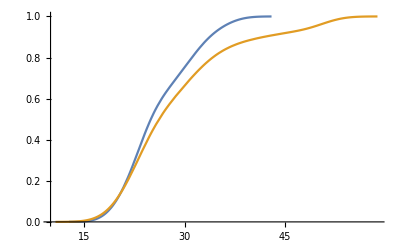

```mathematica
{ansAgeRmOtl,ansAgeRmFarOtl}//SmoothHistogram[#,Automatic,"CDF",AxesOrigin->{10,0}]&
```

分别筛除Med±1.5·QI和Med±3·QI的结果, 分别显示年龄分布呈正偏特征. 进一步分析: 部分受访者填写的年龄数据(介于40a至60a)可能非异常值. 
可能原因推测: 多数(近70%)受访者年龄在20~40岁之间, 少数(近20%)位于40~60岁之间, 考虑到问卷通过网络发布和填写, 这一分布特征与移动互联网用户的年龄特征吻合程度较好.